```mathematica
<<MaTeX`
SetDirectory[NotebookDirectory[]];
Get["MdefineFunctions.wl"]
Get["Mnullgeo4shadow.wl"]
Get["Mplotnullgeos.wl"]
Get["MplotImage.wl"]
Get["Mplot_functions.wl"]
Get["Mazimuthalangle.wl"]
```

## null geodesic

### azimuthal angles

```mathematica
{initot,iniout,inid}=criPhisofb[100000.]
Table[FindRoot[phioutLargeM[lam,Infinity]-(2n-1)Pi/2,{lam,iniout[[n]]}],{n,1,5}]
Table[FindRoot[phitotLargeM[lam,Infinity]-(2n-1)Pi/2,{lam,initot[[n]]0.1}],{n,1,5}]
(*FindRoot[deltaphiLargeM[lam,Infinity]-Pi,{lam,inid}]*)
```

{{0.0461381,0.944776,2.81798,4.33137,4.96917},{0.0481951,1.29512,4.20551,5.13119,5.19409},4.45729}

{{lam→0.0445298},{lam→1.26202},{lam→4.17658},{lam→5.12852},{lam→5.19312}}

{{lam→0.0427227},{lam→0.924231},{lam→2.79269},{lam→4.31751},{lam→4.96479}}

```mathematica
ms=Exp[Range[0,Log[10000],0.1]];
thebs=ParallelTable[criPhisofb[m],{m,ms}];
```

```mathematica
Do[app[m]=ParallelTable[bisection[phioutLargeM[#,ms[[n]]]-(2m-1)Pi/2&,0.01,5.196,10^-8]//Chop,{n,1,Length[ms]}],{m,1,4}]
```

```mathematica
plotmark={Graphics[Disk[{0,0},1]],Tiny};

p2=ListLogLinearPlot[{ms/Sqrt[alpha],thebs[[All,2,2]]}//Transpose,PlotStyle->{RGBColor[{1,0,0}]},PlotMarkers->plotmark,PlotRange->All];
p3=ListLogLinearPlot[{ms/Sqrt[alpha],thebs[[All,2,3]]}//Transpose,PlotStyle->{Blue},PlotMarkers->plotmark,PlotRange->All];
p4=ListLogLinearPlot[{ms/Sqrt[alpha],thebs[[All,2,4]]}//Transpose,PlotStyle->{Orange},PlotMarkers->plotmark,PlotRange->All];

papp2=ListLogLinearPlot[{ms/Sqrt[alpha],app[2]}//Transpose,Joined->True,PlotStyle->{Black},PlotRange->All];
papp3=ListLogLinearPlot[{ms/Sqrt[alpha],app[3]}//Transpose,Joined->True,PlotStyle->{Black},PlotRange->All];
papp4=ListLogLinearPlot[{ms/Sqrt[alpha],app[4]}//Transpose,Joined->True,PlotStyle->{Black},PlotRange->All];
ppi=ListLogLinearPlot[{ms/Sqrt[alpha],thebs[[All,3]]}//Transpose,Joined->True,PlotStyle->RGBColor[{1,0.6,0.2}],PlotRange->All];
(******)

lg1=PointLegend[{Orange,Blue,Red},{MaTeX["\\ b_4'/M",Magnification->1.2],MaTeX["\\ b_3'/M",Magnification->1.2],MaTeX["\\ b_2'/M",Magnification->1.2]},Spacings->0.2,LegendMarkers->plotmark];
lg2=LineLegend[{RGBColor[{1,0.6,0.2}]},{MaTeX["b_\\pi/M",Magnification->1.2],MaTeX["\\text{approximations}",Magnification->1.2]},Spacings->0.2];

ps=Show[{p3,p4,papp3,papp4,ppi,p2,papp2},Epilog->Inset[Framed[Column[{lg1,lg2},Center,Spacings->-1]]
,{6,2.8}],ImageSize->{500,300},PlotRange->All,AxesLabel->{MaTeX["M/\\sqrt{\\alpha}",Magnification->1.4],MaTeX["b/M",Magnification->1.4]},AxesOrigin->{-0.3,1.2}];
{xticks,yticks}=AbsoluteOptions[ps,Ticks][[1,2]];
myticks=change2maTexTicks[xticks,yticks,2,1];
ps=ps/.{Rule[Ticks,_]:>Rule[Ticks,myticks]}
(*Export["/Users/zhangcong/Desktop/latex_tex/paper/LQBHshadow/shadow2/shadow2_paper/cribs.pdf",ps,"PDF"]*)
```

-Graphics-

```mathematica
betav=0.98;
M=√((4 (betav^4) )/(1-betav^2)^3 alpha);
{constants,slope}=gradient4logfit[M];
p1p=myplot[(slope Log[bcri[betav]-#]+constants[[1]])/(Pi)&,MaTeX["b/M"],MaTeX["\\phi/\\pi"],10^-11,bcri[betav]-10^-5,{{10^-11,(bcri[betav]+0.2)},{0,8.5}},1,True,False,{Dashed,Gray,Thickness[0.003]}];
p2p=myplot[(2slope Log[ bcri[betav]-#]+constants[[2]])/(Pi)&,MaTeX["b/M"],MaTeX["\\phi/\\pi"], 10^-11,bcri[betav]-10^-5,{{10^-11,(bcri[betav]+0.2)},{0,8.5}},1,True,False,{Dashed,Gray,Thickness[0.003]}];
p3=myplot[phiout[betav,#][[1]]/(Pi)&,MaTeX["b/M"],MaTeX["\\phi/\\pi"], 10^-11, bcri[betav]-10^-5,{{10^-11,(bcri[betav]+0.2)},{0,8.5}},1,True,False,{Red}];
p4=myplot[phiout[betav,#][[2]]/(Pi)&,MaTeX["b/M"],MaTeX["\\phi/\\pi"],  10^-11,bcri[betav]-10^-5,{{ 10^-11,(bcri[betav]+0.2)},{0,8.5}},1,True,False,{Black}];
p4p5=myplot[(phiout[betav,#][[2]]-phiout[betav,#][[1]])/(Pi)&,MaTeX["b/M"],MaTeX["\\phi/\\pi"],  10^-11, bcri[betav]-10^-5,{{ 10^-11,(bcri[betav]+0.2)},{0,8.5}},1,True,False,{Black,DotDashed}];
p5=Show[{p1p,p2p,p4,p3,p4p5}];
p6=Legended[p5,Placed[Framed[LineLegend[{Black,Red,DotDashed},{MaTeX["\\phi_{\\text{tot}}"],MaTeX["\\phi_{\\text{out}}"],MaTeX["\\Delta\\phi"]},Spacings->0.15]],{0.5,0.8}]]
(*Export["/Users/zhangcong/Desktop/latex_tex/paper/LQBHshadow/shadow2/shadow2_paper2/phivalue.pdf",p6,"PDF"]*)
```

-Graphics-

### typical geodesics

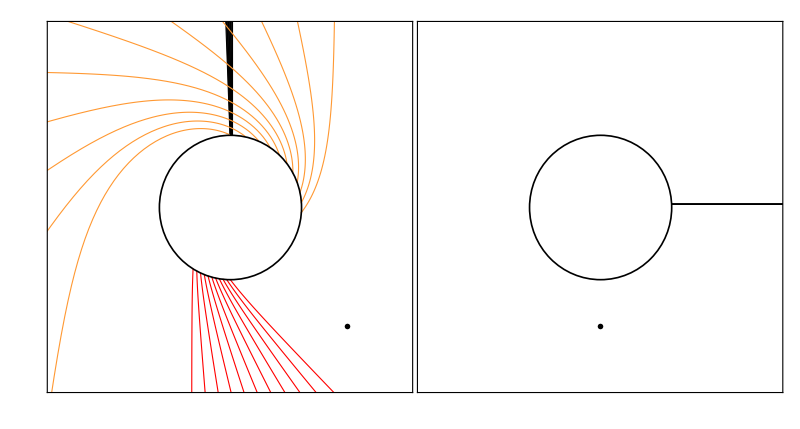

/Users/zhangcong/Desktop/latex_tex/paper/LQBHshadow/shadow2/shadow2_paper2/nullgeos.pdf

```mathematica
plot=Plot[phiout[M,b],{b, 10^-11,bcri[M]-10^-5},PlotRange->All];
data=Cases[plot,_Line,Infinity];
data=List@@@data//Flatten[#,1]&;
fit1=Interpolation[data[[1]]];
fit2=Interpolation[data[[2]]];
xrange=fit1[[1,1]];
b2=Table[bisection[fit2[#]-Pi/2-n Pi&,xrange[[1]],xrange[[2]],10^-8],{n,0,4}];
b1=Table[bisection[fit1[#]-Pi/2-n Pi&,xrange[[1]],xrange[[2]],10^-8],{n,0,4}];
rangeb=MapThread[Range[#1,#2,(#2-#1)/10]&,{b2,b1}];
color={Black,Red,RGBColor[1,0.6,0.2],Blue};
plotrange=1300/263.;
p0=Plot[{},{x,-plotrange,plotrange},PlotStyle->White];
thetickes=maTexTicks[{{-plotrange,plotrange},{-plotrange,plotrange}},{Identity,Identity},{Identity,Identity},1,True,False];
p0=p0/.{Rule[FrameTicks,_]:>Rule[FrameTicks,{{thetickes[[2]],Automatic},{thetickes[[1]],Automatic}}]};
p1=Show[{p0,
Table[plotgeo[b,M,{Thickness[0.002],color[[1]]}],{b,rangeb[[1]]}],
Table[plotgeo[b,M,{Thickness[0.002],color[[2]]}],{b,rangeb[[2]]}],
Table[plotgeo[b,M,{Thickness[0.002],color[[3]]}],{b,rangeb[[3]]}],
Graphics[{
{Thickness[0.003],Circle[{0,0},horizons[M][[2]]]},
Inset[MaTeX["A \\text{ Region}",Magnification->1.2],{0,-plotrange 2/3}]
}
]
},
Frame->True,Axes->False,PlotRange->{{-plotrange,plotrange},{-plotrange,plotrange}},
ImagePadding->{{Automatic,Automatic}, {Automatic,30}},AspectRatio->1
];
p0=Plot[{},{x,-plotrange,plotrange},PlotStyle->White];
thetickes=maTexTicks[{{-plotrange,plotrange},{-plotrange,plotrange}},{Identity,Identity},{Identity,Identity},1,True];
p0=p0/.{Rule[FrameTicks,_]:>Rule[FrameTicks,{{thetickes[[2]],Automatic},{thetickes[[1]],Automatic}}]};
p2=Show[{p0,
Table[plotgeop[b,M,{Thickness[0.002],color[[1]]}],{b,rangeb[[1]]}],
Table[plotgeop[b,M,{Thickness[0.002],color[[2]]}],{b,rangeb[[2]]}],
Table[plotgeop[b,M,{Thickness[0.002],color[[3]]}],{b,rangeb[[3]]}],
Graphics[{{Thickness[0.003],Circle[{0,0},horizons[M][[2]]]},
,
Inset[MaTeX["A' \\text{ Region}",Magnification->1.2],{3.3,-plotrange 2/3}]
}](*,
ParametricPlot[{0,y},{y,horizons[betav][[2]],6},PlotStyle->{DotDashed,Thickness[0.003],Black}],
ParametricPlot[{0,y},{y,-horizons[betav][[2]],-6},PlotStyle->{DotDashed,Thickness[0.003],Black}]*)
},
Frame->True,Axes->False,PlotRange->{{-plotrange,plotrange},{-plotrange,plotrange}},AspectRatio->1
];
p3=GraphicsGrid[{{p2,p1}},Spacings->-50]
Export["/Users/zhangcong/Desktop/latex_tex/paper/LQBHshadow/shadow2/shadow2_paper2/nullgeos.pdf",p3,"PDF"]
```

```mathematica
FrameLabel
```

### Shadow Image

```mathematica
betav=0.98;
M=√((4 (betav^4) )/(1-betav^2)^3 alpha)
Iemo[r_,M_]:=If[r>1/umin[M],(1/(r-(1/umin[M]-1))^3),0]
emissionbs=criPhisofb[M,0,4]
```

263.239

{{0.0715482,1.07743,2.97386,4.41407,4.99477},{0.0758542,1.51209,4.37333,5.14566,5.19416},4.45728}

```mathematica
Do[phioutexpl[m]=bisection[phioutLargeM[#,M]-(2m-1)Pi/2&,0.01,5.196,10^-8]//Chop,{m,1,4}]
```

```mathematica
Do[phitotexpl[m]=bisection[phitotLargeM[#,M]-(2m-1)Pi/2&,0.01,5.196,10^-8]//Chop,{m,1,4}]
```

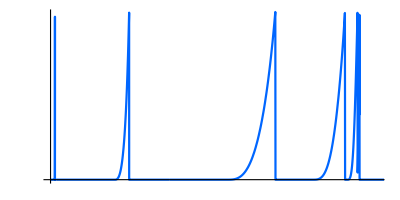

```mathematica
xrange=8.5;
p0e=Plot[-0.1,{x,0,xrange},PlotRange->{{0,xrange},{0.,1}},PlotStyle->Directive[Opacity[0]],AxesLabel->{MaTeX["r/M",Magnification->1.4],MaTeX["I_{\\rm em}/I_0",Magnification->1.4]}];
thetickes=maTexTicks[{{0,xrange},{0.,1}},{Identity,Identity},{Identity,Identity},3,True,True,1.4]/.AbsoluteThickness[x_]:>AbsoluteThickness[5x];
p0e=p0e/.{Rule[Ticks,_]:>Rule[Ticks,thetickes]};
pe=Plot[Iemo[r ,M],{r,0,xrange},PlotRange->All,PlotStyle->Black,AspectRatio->1/2];
se=Show[{p0e,pe},AspectRatio->1/2,ImageSize->{400,200}];
p1=Plot[Iob[Iemo[#,M]&,_,b ,M,"Wh"],{b,0,0.1},PlotRange->All,PlotStyle->RGBColor[0,0.4,1]];
p1p=Plot[Iob[Iemo[#,M]&,_,b,M,"Wh"],{b,0.1,2},PlotRange->All,PlotStyle->RGBColor[0,0.4,1]];
p1pp=Plot[Iob[Iemo[#,M]&,_, b,M,"Wh"],{b,2,12},PlotRange->All,PlotStyle->RGBColor[0,0.4,1]];
xrange=5.5;
p0=Plot[-0.1,{x,0,xrange},PlotStyle->Directive[Opacity[0]],AxesLabel->{MaTeX["b/M",Magnification->1.4],MaTeX["I^{\\rm obs}/I_0",Magnification->1.4]},PlotRange->{{0,xrange},{0.,0.11}}];
thetickes=maTexTicks[{{0,xrange},{0.,0.11}},{Identity,Identity},{Identity,Identity},3,True,True,1.4]/.AbsoluteThickness[x_]:>AbsoluteThickness[5x];
p0=p0/.{Rule[Ticks,_]:>Rule[Ticks,thetickes]};
so1=Show[{p0,p1,p1p,p1pp},ImageSize->{400,200},AspectRatio->1/2]
```

```mathematica
Iobb=List@@(Cases[p1,_Line,Infinity]//First)//First//Chop;
Iobb=Join[Iobb,List@@(Cases[p1p,_Line,Infinity]//First)//First//Chop];
Iobb=Join[Iobb,List@@(Cases[p1pp,_Line,Infinity]//First)//First//Chop];
Iobbp=Tuples[{Iobb,Range[0,2Pi,Pi/50]}];
Iobbp=ParallelMap[{#[[1,1]]Cos[#[[2]]],#[[1,1]]Sin[#[[2]]],#[[1,2]]}&,Iobbp];
plotrange=0.08;
s20=ListDensityPlot[Iobbp,ColorFunction->(ColorData[{"SunsetColors",{0,0.15}}]),ColorFunctionScaling->False,PlotLegends->None,ImageSize->{180,180},Frame->False,PlotRange->{{-plotrange,plotrange},{-plotrange,plotrange}}];
plotrange=5.5;
s21=ListDensityPlot[Iobbp,ColorFunction->(ColorData[{"SunsetColors",{0,0.15}}]),ColorFunctionScaling->False,PlotLegends->None,ImageSize->{250,250},Frame->False,PlotRange->{{-plotrange,plotrange},{-plotrange,plotrange}}];
```

```mathematica
s1=GraphicsGrid[{{se},{so1}},Spacings->-0];
s2p=GraphicsGrid[{{s20},{s21}},Spacings->-10,ImageSize->{200,350}];
s2p=Show[{s2p,Graphics[{
{Directive[White,Dashed,Thick],Line[{{117.3,-358.5},{43,-234}}]},
{Directive[Black,Dashed,Thick],Line[{{43,-234},{28,-210}}]},
{Directive[White,Dashed,Thick],Line[{{121.3,-358.5},{197,-233}}]},
{Directive[Black,Dashed,Thick],Line[{{197,-233},{210,-210}}]}
}]}];
```

```mathematica
s3=GraphicsGrid[{{s1,s2p}},Spacings->-80,ImageSize->{1000,700},Alignment->Center]
(*Export["/Users/zhangcong/Desktop/latex_tex/paper/LQBHshadow/shadow2/shadow2_paper/shadow.eps",s3,"EPS",ImageSize->{1000,700},ImageResolution->800]*)
```

-Graphics-

```mathematica
pbh=Plot[Iob[_,Iemo[#,M]&,b,M,"Bh"],{b,0,12},PlotRange->All,PlotStyle->{Red,Dashed}];
Iobbh=List@@(Cases[pbh,_Line,Infinity]//First)//First//Chop;
Iobbhp=Tuples[{Iobbh,Range[0,2Pi,Pi/50]}];
Iobbhp=ParallelMap[{#[[1,1]]Cos[#[[2]]],#[[1,1]]Sin[#[[2]]],#[[1,2]]}&,Iobbhp];
plotrange=5.5;
sbh=ListDensityPlot[Iobbhp,ColorFunction->(ColorData[{"SunsetColors",{0,0.15}}]),ColorFunctionScaling->False,PlotLegends->None,ImageSize->{200,200},Frame->False,PlotRange->{{-plotrange,plotrange},{-plotrange,plotrange}}];
```

```mathematica
p1bwh=Plot[Iob[Iemo[#,M]&,Iemo[#,M]&,b ,M,"Bh-Wh"],{b,0,0.1},PlotRange->All,PlotStyle->RGBColor[0,0.4,1]];
p1bwhp=Plot[Iob[Iemo[#,M]&,Iemo[#,M]&,b ,M,"Bh-Wh"],{b,0.1,2},PlotRange->All,PlotStyle->RGBColor[0,0.4,1]];
p1bwhpp=Plot[Iob[Iemo[#,M]&,Iemo[#,M]&,b ,M,"Bh-Wh"],{b,2,12},PlotRange->All,PlotStyle->RGBColor[0,0.4,1]];
```

```mathematica
Iobbwh=List@@(Cases[p1bwh,_Line,Infinity]//First)//First//Chop;
Iobbwh=Join[Iobbwh,List@@(Cases[p1bwhp,_Line,Infinity]//First)//First//Chop];
Iobbwh=Join[Iobbwh,List@@(Cases[p1bwhpp,_Line,Infinity]//First)//First//Chop];
```

```mathematica
Iobbwhp=Tuples[{Iobbwh,Range[0,2Pi,Pi/50]}];
Iobbwhp=ParallelMap[{#[[1,1]]Cos[#[[2]]],#[[1,1]]Sin[#[[2]]],#[[1,2]]}&,Iobbwhp];
plotrange=0.08;
swbh0=ListDensityPlot[Iobbwhp,ColorFunction->(ColorData[{"SunsetColors",{0,0.15}}]),ColorFunctionScaling->False,PlotLegends->None,ImageSize->{120,120},Frame->False,PlotRange->{{-plotrange,plotrange},{-plotrange,plotrange}}];
plotrange=5.5;
swbh=ListDensityPlot[Iobbwhp,ColorFunction->(ColorData[{"SunsetColors",{0,0.15}}]),ColorFunctionScaling->False,PlotLegends->None,ImageSize->{250,250},Frame->False,PlotRange->{{-plotrange,plotrange},{-plotrange,plotrange}}];
```

```mathematica
swbh2=GraphicsGrid[{{swbh0},{swbh}},Spacings->-45,ImageSize->{200,350}];
swbh2=Show[{swbh2,Graphics[{
{Directive[White,Dashed,Thick],Line[{{100.,-306.2},{47.5,-181.}}]},
{Directive[Black,Dashed,Thick],Line[{{47.5,-181.},{40.87,-163.7}}]},
{Directive[White,Dashed,Thick],Line[{{104,-306.2},{155,-181}}]},
{Directive[Black,Dashed,Thick],Line[{{155,-181},{161.9,-163.7}}]}
}]}];
```

```mathematica
plotrange=0.08;
s20=ListDensityPlot[Iobbp,ColorFunction->(ColorData[{"SunsetColors",{0,0.15}}]),ColorFunctionScaling->False,PlotLegends->None,ImageSize->{120,120},Frame->False,PlotRange->{{-plotrange,plotrange},{-plotrange,plotrange}}];
plotrange=5.5;
s21=ListDensityPlot[Iobbp,ColorFunction->(ColorData[{"SunsetColors",{0,0.15}}]),ColorFunctionScaling->False,PlotLegends->None,ImageSize->{250,250},Frame->False,PlotRange->{{-plotrange,plotrange},{-plotrange,plotrange}}];
```

```mathematica
se=Show[p0e,pe,AspectRatio->0.5,ImageSize->{400,200}];
so1=Show[{p0,p1,p1p,p1pp},ImageSize->{400,200},AspectRatio->0.5];
s1=GraphicsGrid[{{se},{so1}},Spacings->-0];
s2p=GraphicsGrid[{{s20},{s21}},Spacings->-45,ImageSize->{400,220}];
s2p=Show[{s2p,Graphics[{
{Directive[White,Dashed,Thick],Line[{{100.,-306.2},{47.5,-181.}}]},
{Directive[Black,Dashed,Thick],Line[{{47.5,-181.},{40.87,-163.7}}]},
{Directive[White,Dashed,Thick],Line[{{104,-306.2},{155,-181}}]},
{Directive[Black,Dashed,Thick],Line[{{155,-181},{161.9,-163.7}}]}
}]}];
```

```mathematica
s3p=GraphicsGrid[{{s1,s2p}},Spacings->-140,ImageSize->{900,500},Alignment->Center];
sbbwh=GraphicsGrid[{{sbh},{swbh2}},Spacings->-80,ImageSize->{250,500},Alignment->Center];
```

```mathematica
stot=GraphicsGrid[{{s3p,sbbwh}},Spacings->-490,ImageSize->{800,400},Alignment->Center]
(*Export["/Users/zhangcong/Desktop/latex_tex/paper/LQBHshadow/shadow2/shadow2_paper2/shadowtot.eps",stot,"EPS",ImageSize->{800,400},ImageResolution->800]*)
```

-Graphics-